```mathematica
f[n_,x_]:=n/;1/n≤x<2/n;
```

```mathematica
f[n_,x_]:=0/;x≥2/n;
```

```mathematica
f[n_,x_]:=0/;x<1/n;
```

```mathematica
f[2,3]
```

f[2,3]

```mathematica
f[2,3/4]
```

2

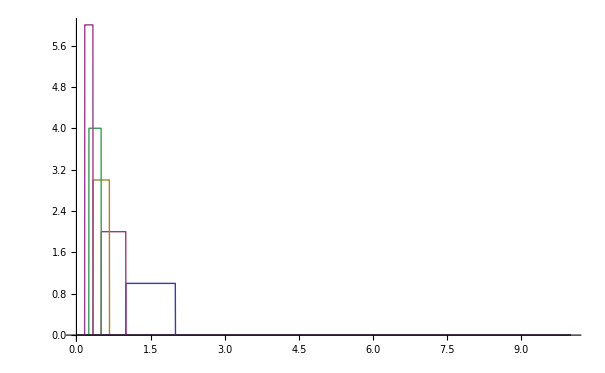

```mathematica
Plot[{f[1,b],f[2,b],f[3,b],f[4,b],f[5,b],f[6,b]},{b,0,10}]
```